```mathematica
(*this is for the correlator*)
```

```mathematica
ClearAll["Global`*"]
```

### (a) the correlator evolution

```mathematica
(*solve the correlator evolution*)
A0=-0.3;
β=1;
Correlator[γ_,A_,ω_,q_]:=Module[{T,t0,t0sol,t1,t1sol,t2,t2sol,Λ,n,m,nt,mt,mt1,G2sol,g2,g3sol,g3,g4sol,g4,λ,λ1,ωt,γnF,γmF,γmF1,colsol},T=2π/ω;
(*Solve t2*)
t2sol=NDSolve[{Rt2'[x]+q/2(A0+A Cos[ω x]) -2 It2[x]q(1+A0+A Cos[ω x])-2(Rt2[x]^2-It2[x]^2)q (A0+A Cos[ω x])==0,It2'[x]+2 Rt2[x]q(1+A0+A Cos[ω x])- 4(Rt2[x]It2[x]) q (A0+A Cos[ω x])==0,Rt2[0]==Rt2[T],It2[0]==It2[T]},{Rt2,It2},{x,0,4T}];
t2[t_]:=(Rt2[t]/.t2sol[[1,1]])+I(It2[t]/.t2sol[[1,2]]);
(*Solve t1*)
t1sol=NDSolve[{y'[x]+(1+8y[x]t2[x])q/2(A0+A Cos[ω x])-2I q(1+A0+A Cos[ω x])y[x]==0,y[0]==y[T]},{y},{x,0,4T}];
t1[t_]:=y[t]/.t1sol[[1]];
(*Solve Λ*)
Λ=1/T NIntegrate[(1+A0+A Cos[ω x])+2I (A0+A Cos[ω x])t2[x],{x,0,T}];
(*Solve t0*)
t0sol=NDSolve[{y'[x]+q(1+A0+A Cos[ω x])+2I q(A0+A Cos[ω x])t2[x]==0,y[0]==0},y,{x,0,4T}];
t0[t_]:=(y[t]/.t0sol[[1]])+q Λ t;
(*Define n&m*)
n[t_]:=-1/2+(1+A0+A Cos[ω t])/(2 √(1+2(A0+A Cos[ω t])))Coth[(β q)/2 √(1+2(A0+A Cos[ω t]))];
m[t_]:=-(A0+A Cos[ω t])/(2 √(1+2(A0+A Cos[ω t])))Coth[(β q)/2 √(1+2(A0+A Cos[ω t]))];
(*Define nt, mt & mt1*)
nt[t_?NumericQ]:=Evaluate@-1/2+(n[t]+1/2)(1+8t1[t]t2[t])+2I t1[t]m[t]-2I t2[t](1+4t1[t]t2[t])m[t];
mt[t_?NumericQ]:=Evaluate@Exp[-2I t0[t]](m[t]-4I t2[t](n[t]+1/2)-4t2[t]^2 m[t]);
mt1[t_?NumericQ]:=Evaluate@Exp[2I t0[t]](m[t](1+4t1[t]t2[t])^2+4I t1[t](1+4t1[t]t2[t])(n[t]+1/2)-4t1[t]^2m[t]);
(*Solve g2*)
G2sol=NDSolve[{y'[x]+γ q(1+Cos[ω x])y[x]-γ q(1+Cos[ω x])(nt[x]+1/2)==0,y[0]==y[T]},{y},{x,0,4T}];
g2[t_]:=-Log[(y[t]/.G2sol[[1,1]])+1/2]; 
(*Solve g3*)
g3sol=NDSolve[{y'[x]+(γ q(1+Cos[ω x])+2I Λ q)y[x]-γ q(1+Cos[ω x])mt[x]==0,y[0]==y[T]},{y},{x,0,4T}];
g3[t_]:=y[t]/.g3sol[[1]];
(*Solve g4*)
g4sol=NDSolve[{y'[x]+(γ q(1+Cos[ω x])-2I Λ q)y[x]-γ q(1+Cos[ω x])mt1[x]==0,y[0]==y[T]},{y},{x,0,4T}];
g4[t_]:=y[t]/.g4sol[[1]];
λ=4 I t1[0] Λ;
λ1=-4I t2[0](1+4t1[0] t2[0])Λ;
ωt=Λ(1+8 t1[0] t2[0]);
(*here we use t0[0]=0*)
γnF=-γ/2+γ(1+8t1[0]t2[0])(Exp[-g2[0]]-1/2)-2I g3[0] t1[0] (1+4t1[0] t2[0])(γ+2I Λ)+ 2I g4[0] t2[0](γ-2I Λ);
γmF=4γ I t2[0](Exp[-g2[0]]-1/2)(1+4t1[0] t2[0])-4g4[0] t2[0]^2(γ-2I Λ)+g3[0] (1+4t1[0] t2[0])^2(γ+2I Λ);
γmF1=-4I γ t1[0](Exp[-g2[0]]-1/2)+g4[0](γ-2I Λ)-4g3[0] t1[0]^2 (γ+2I Λ);
colsol=NDSolve[{n1'[t]==q(I λ m1[t]-I λ1 m2[t]+γnF-γ n1[t]),n2'[t]==q(I λ m1[t]-I λ1 m2[t]+γnF-γ n2[t]),m1'[t]==q((-2I ωt-γ) m1[t]-I λ1(1+n1[t]+n2[t])+γmF),m2'[t]==q((2I ωt-γ) m2[t]+I λ(1+n1[t]+n2[t])+γmF1),n1[0]==0,n2[0]==0,m1[0]==0,m2[0]==0},{n1,n2,m1,m2},{t,0,20T}];
{colsol,T,γ-2Abs[Im[Λ]]}];
```

```mathematica
Evolution[pack_]:=Module[{sols,tw,stab},{sols,tw,stab}=pack;Table[{s,Evaluate@Re[n1[s]/.sols[[1,1]]]},{s,0,20tw,tw}]]
```

```mathematica
cv1=Evolution[Correlator[0.1,0.1,1.2,1]];
cv2=Evolution[Correlator[0.12,0.1,1.2,1]];
cv3=Evolution[Correlator[0.13,0.1,1.2,1]];
cv4=Evolution[Correlator[0.15,0.1,1.2,1]];
cv5=Evolution[Correlator[0.18,0.1,1.2,1]];
cv6=Evolution[Correlator[0.2,0.1,1.2,1]];
```

```mathematica
(*plots for <a^+a>*)
```

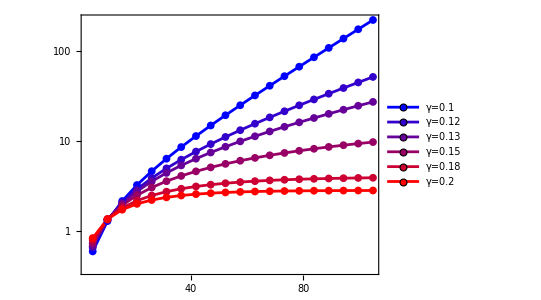

```mathematica
Show[ListLogPlot[{cv1,cv2,cv3,cv4,cv5,cv6},
PlotRange->Full,AspectRatio->0.75,
PlotStyle->{Blend[{Blue,Red},0],Blend[{Blue,Red},1/5],Blend[{Blue,Red},2/5],Blend[{Blue,Red},3/5],Blend[{Blue,Red},4/5],Blend[{Blue,Red},1]},
PlotMarkers->{Graphics[{Disk[]}],8},
PlotLegends->Placed[LineLegend[{"γ=0.1", "γ=0.12","γ=0.13","γ=0.15","γ=0.18","γ=0.2"},LabelStyle->{FontSize->13}],{0.15, 0.7}],
FrameTicks->{{Table[{10^n,Superscript[10,n]},{n,-1,2}],None},{Range[0,100,20],None}},
FrameTicksStyle->Directive[Black,20],
FrameStyle->AbsoluteThickness[1.5],
Frame->True,Joined->True]]
```

### (b) the decay rate vs gamma

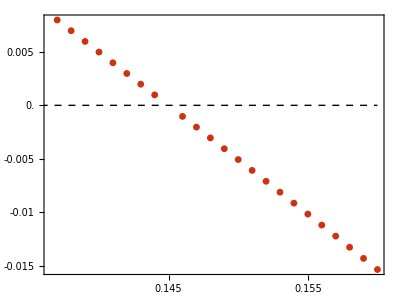

```mathematica
(*Plot the curve for the decay rate b*)
(*A=0.1,ω=1.2*)
γlist=Table[i,{i,0.146,0.16,0.001}]~Join~{0.144,0.143,0.142,0.141,0.14,0.139,0.138,0.137};
decaylist={-0.001032,-0.002037,-0.003044,-0.004053,-0.005065,-0.006079,-0.007096,-0.008116,-0.009139,-0.01016,-0.01119,-0.01222,-0.01326,-0.01430,-0.01534}~Join~{0.0009743,0.001976,0.002977,0.003978,0.004979,0.005972,0.006974,0.007975};
ListPlot[Transpose[{γlist,decaylist}],
PlotRange->Full,AspectRatio->0.75,
PlotMarkers->{Graphics[{Disk[]}],7},
PlotStyle->RGBColor["#CC3311"],
Epilog->{{Black,Dashed,Line[{{0.13,0},{0.16,0}}]}},
FrameTicks->{{Range[-0.02,0.01,0.005],None},{Range[0.135,0.16,0.005],None}},
FrameTicksStyle->Directive[Black,18],
FrameStyle->AbsoluteThickness[1.5],
Frame->True]
```